Definicje funkcji używanych przy mapowaniu:

```mathematica
GetMax[x_] :={First[x], Max[Take[x,{2,Length[x]}]]};
GetMean[x_] :={First[x], Mean[Take[x,{2,Length[x]}]]};
GetVariance[x_] :={First[x], Variance[Take[x,{2,Length[x]}]]};
GetPlusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] + StandardDeviation[Take[x,{2,Length[x]}]]};
GetMinusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] - StandardDeviation[Take[x,{2,Length[x]}]]};
```

```mathematica
UNI :="uniform"; MIN := "minimum"; AGL := "always_go_left";
Strategies := {UNI, MIN, AGL};
CCP := "coupon_collector"; BPP := "birthday_paradox"; MLP := "max_load";
Problems := {CCP, BPP, MLP};
RawResults[s_,p_,d_] := ReadList[StringJoin["/home/dev/Workspaces/Studies/AnalAlgo/BallsAndCups/cups_" ,s,"_",p,"_",ToString[d],".m"], Number, RecordLists->True];
ResultsMax[s_,p_,d_] := Map[GetMax, RawResults[s,p,d]];
ResultsMean[s_,p_,d_] := Map[GetMean,  RawResults[s,p,d]];
ResultsVariance[s_,p_,d_] := Map[GetVariance,  RawResults[s,p,d]];
ResultsPlusStandardDeviation[s_,p_,d_] := Map[GetPlusStandardDeviation,  RawResults[s,p,d]];
ResultsMinusStandardDeviation[s_,p_,d_] := Map[GetMinusStandardDeviation,  RawResults[s,p,d]];
```

Wyświetlanie wyników dla Coupon Collector Problem z użyciem rozkładu jednostajnego:

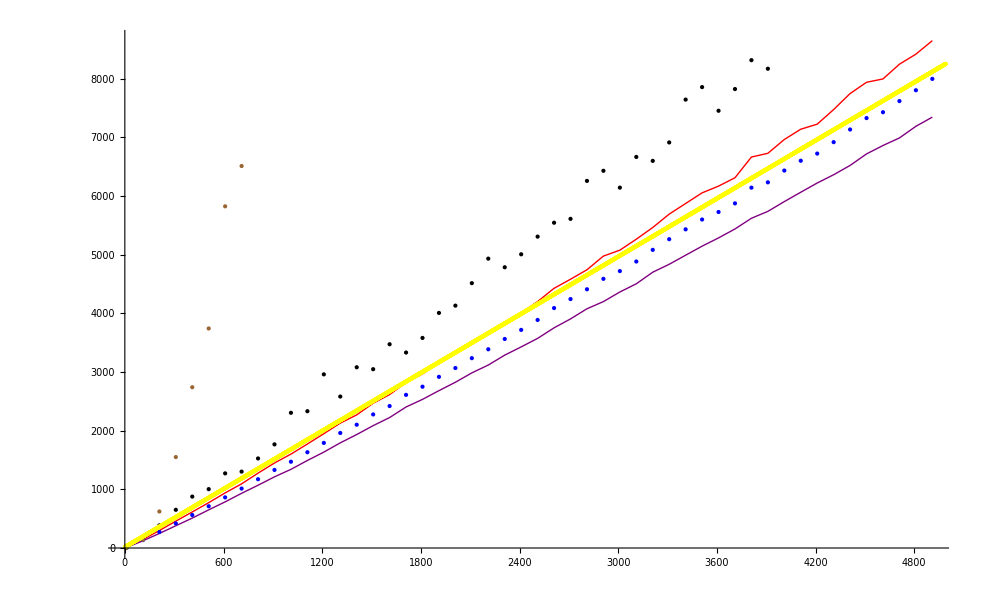

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[AGL,CCP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[AGL,CCP,10],PlotStyle->Purple],
ListPlot[ResultsMax[AGL,CCP,10],PlotStyle -> Black],
ListPlot[ResultsMean[AGL,CCP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[AGL,CCP,10], PlotStyle->Brown],
ListPlot[Table[1.65n,{n, 10, 5000}], PlotStyle-> Yellow]
]
```

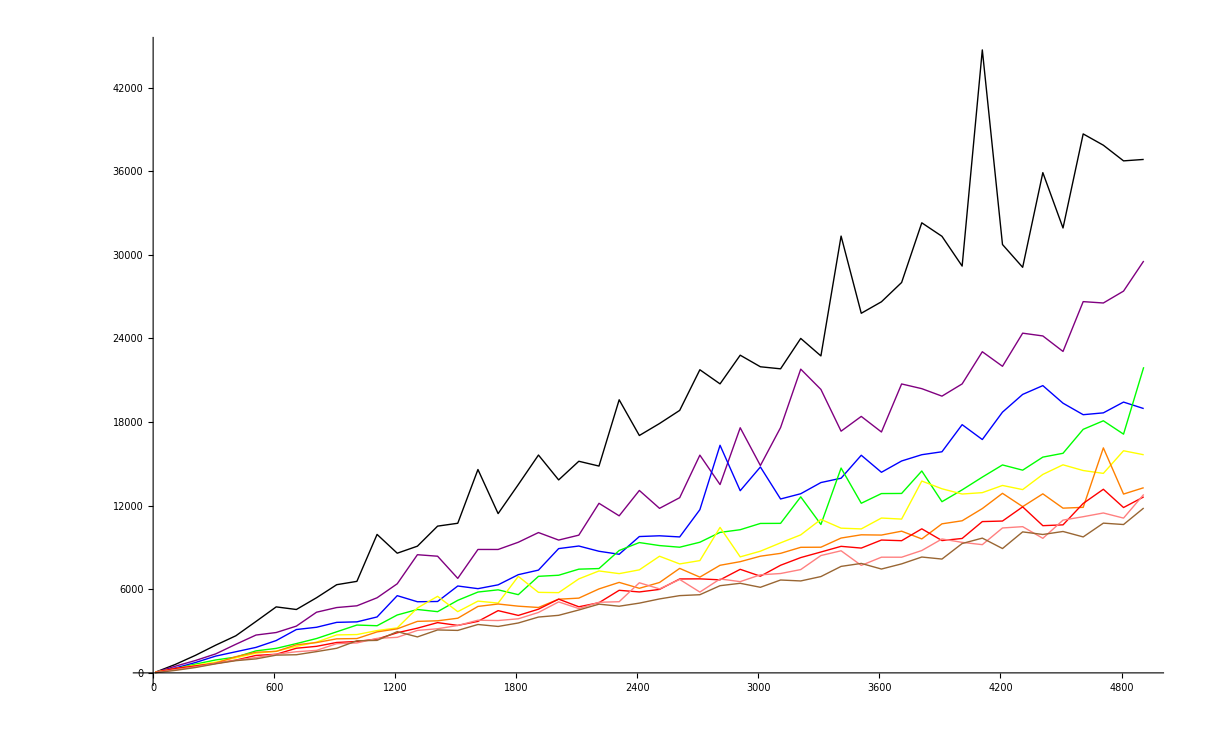

```mathematica
Show[
ListLinePlot[ResultsMax[AGL,CCP,2],PlotStyle -> Black],
ListLinePlot[ResultsMax[AGL,CCP,3],PlotStyle -> Purple],
ListLinePlot[ResultsMax[AGL,CCP,4],PlotStyle -> Blue],
ListLinePlot[ResultsMax[AGL,CCP,5],PlotStyle -> Green],
ListLinePlot[ResultsMax[AGL,CCP,6],PlotStyle -> Yellow],
ListLinePlot[ResultsMax[AGL,CCP,7],PlotStyle -> Orange],
ListLinePlot[ResultsMax[AGL,CCP,8],PlotStyle -> Red],
ListLinePlot[ResultsMax[AGL,CCP,9],PlotStyle -> Pink],
ListLinePlot[ResultsMax[AGL,CCP,10],PlotStyle -> Brown]
]
```

Wyświetlanie wyników dla Birthday Paradox Problem z użyciem rozkładu jednostajnego:

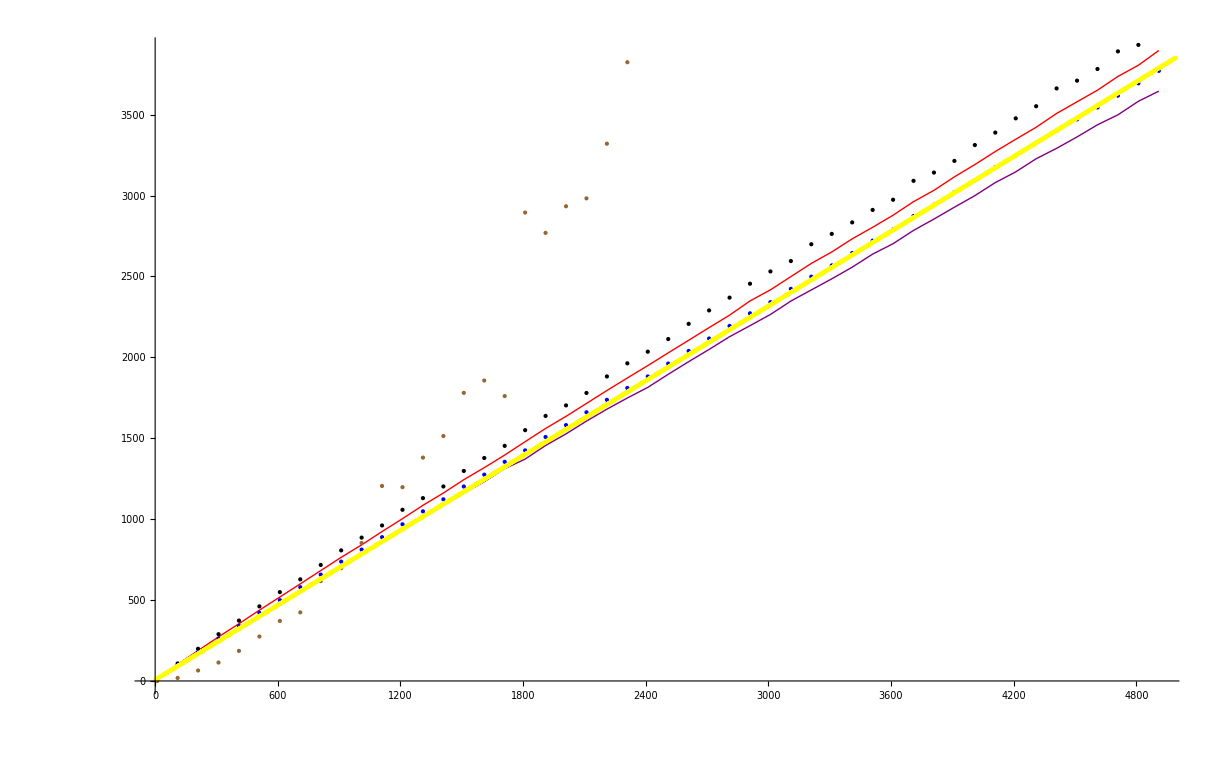

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[AGL,BPP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[AGL,BPP,10],PlotStyle->Purple],
ListPlot[ResultsMax[AGL,BPP,10],PlotStyle -> Black],
ListPlot[ResultsMean[AGL,BPP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[AGL,BPP,10], PlotStyle->Brown],
ListPlot[Table[0.77n,{n, 10, 5000}], PlotStyle-> Yellow]
]
```

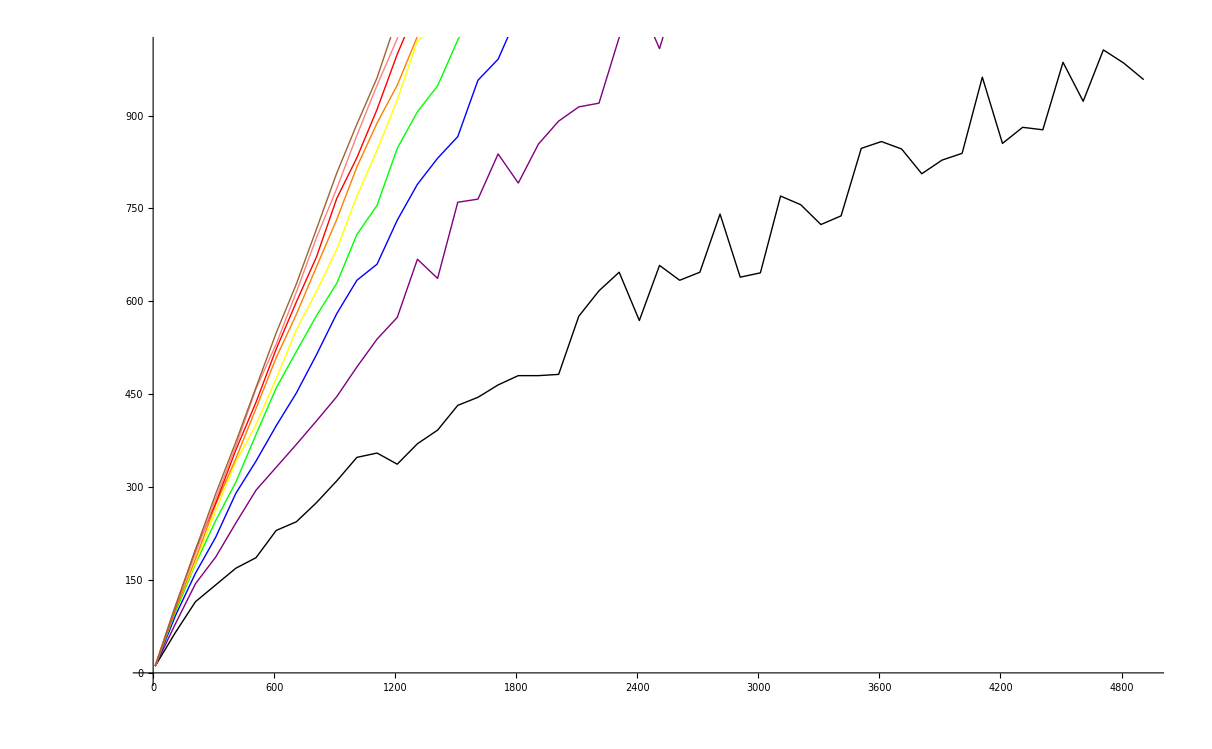

```mathematica
Show[
ListLinePlot[ResultsMax[AGL,BPP,2],PlotStyle -> Black],
ListLinePlot[ResultsMax[AGL,BPP,3],PlotStyle -> Purple],
ListLinePlot[ResultsMax[AGL,BPP,4],PlotStyle -> Blue],
ListLinePlot[ResultsMax[AGL,BPP,5],PlotStyle -> Green],
ListLinePlot[ResultsMax[AGL,BPP,6],PlotStyle -> Yellow],
ListLinePlot[ResultsMax[AGL,BPP,7],PlotStyle -> Orange],
ListLinePlot[ResultsMax[AGL,BPP,8],PlotStyle -> Red],
ListLinePlot[ResultsMax[AGL,BPP,9],PlotStyle -> Pink],
ListLinePlot[ResultsMax[AGL,BPP,10],PlotStyle -> Brown]
]
```

Wyświetlanie wyników dla Max Load Problem z użyciem rozkładu jednostajnego:

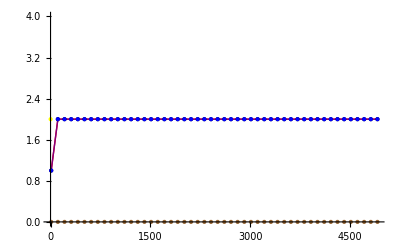

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[AGL,MLP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[AGL,MLP,10],PlotStyle->Purple],
ListPlot[ResultsMax[AGL,MLP,10],PlotStyle -> Black],
ListPlot[ResultsMean[AGL,MLP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[AGL,MLP,10], PlotStyle->Brown],
ListPlot[Table[2,{n,0,100, 5000}], PlotStyle-> Yellow]
]
```

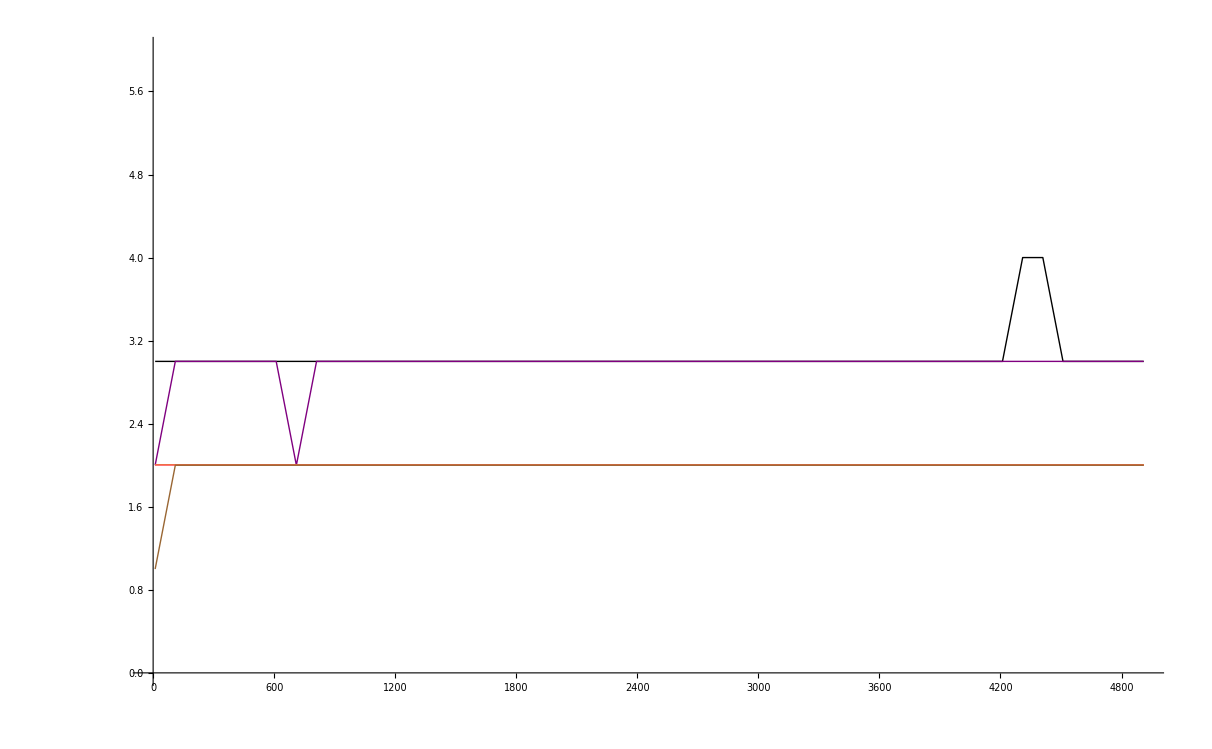

```mathematica
Show[
ListLinePlot[ResultsMax[AGL,MLP,2],PlotStyle -> Black],
ListLinePlot[ResultsMax[AGL,MLP,3],PlotStyle -> Purple],
ListLinePlot[ResultsMax[AGL,MLP,4],PlotStyle -> Blue],
ListLinePlot[ResultsMax[AGL,MLP,5],PlotStyle -> Green],
ListLinePlot[ResultsMax[AGL,MLP,6],PlotStyle -> Yellow],
ListLinePlot[ResultsMax[AGL,MLP,7],PlotStyle -> Orange],
ListLinePlot[ResultsMax[AGL,MLP,8],PlotStyle -> Red],
ListLinePlot[ResultsMax[AGL,MLP,9],PlotStyle -> Pink],
ListLinePlot[ResultsMax[AGL,MLP,10],PlotStyle -> Brown]
]
```